# Fully implicit scheme for staircase voltammetry

## - using expanding space grid

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
xTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

yTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

xTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];

yTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.7]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(*options for voltammograms*)

optionA={
FrameTicks-> {Automatic,yTicks2,Automatic,yTicks4},
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
StyleForm["increment",FontFamily->"Arial" ,FontSize-> 12,FontColor->Black],StyleForm["χ",FontFamily-> "Times New Roman" ,FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
(*options for voltammograms*)

optionB={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks:>  {xTicks1,yTicks2,xTicks3,yTicks4},
FrameLabel->{
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],
StyleForm["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}
};
```

```mathematica
optionD={
FrameTicks-> {xTicks1,yTicks2,xTicks3,yTicks4},
FrameLabel->{
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
StyleForm["χ",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain"],
None,
None},
PlotRange:>  {{upperLimit,lowerLimit},{Min[squareDiff⟦All,2⟧]-.1,Max[squareBack⟦All,2⟧]+.1}},Epilog:>  {Text["χ_b",{0,Max[squareBack⟦All,2⟧]-.1}],Text["χ_f",{0,Min[squareFor⟦All,2⟧]+.1}],Text["Δχ",{0,Min[squareDiff⟦All,2⟧]+.1}]}
};
```

```mathematica
(*options for power spectrum plots*)

optionMain={
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameTicks->Automatic,FrameLabel->{"Frequency",None,None,None}};
```

```mathematica
dcOptions={
Joined-> True,
PlotStyle->{Red,Thickness[0.003]},FrameTicks-> Automatic,
FrameLabel-> {
StyleForm["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
StyleForm["√πχ",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain"],
None,
None}};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals2];

makeVarDiagonals2[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]
```

## Set Up Solution

```mathematica
Clear[solveCV];

solveCV[list_List,k_Integer]:=Module[{temp,b,bot,temp2,ξ},

ξ=Exp[α*(upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)))];

bot=1./(3.+ ksStar*(ξ^-1+ξ));

b=Take[conc,{2,m-1}];
b⟦1⟧+=(bot*𝔻*ksStar*ξ);
b⟦m-2⟧+=𝔻*a^(5-2*m);

y⟦1⟧=y1-4.*𝔻*bot;
z⟦1⟧=z1+𝔻*bot;

temp2=tridiagonalSolve [x,y,z,b];

conc=Flatten[{(ksStar*ξ+4.*temp2⟦1⟧-temp2⟦2⟧)*bot,temp2,1.}];Take[conc,3]];
```

```mathematica
Clear[implicitSolveStaircase];

implicitSolveStaircase[m_Integer,n_Integer,d_,{upperLimit_,ksStar_,α_},{Δ𝔼s_,tN_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,solveNext},

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,tmp3},

ξ=Exp[α*(upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)))];
tmp=1./(3.+ ksStar*(ξ^-1+ξ));
(*tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));*)

b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ);
(*b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));*)
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
tmp3=Flatten[{(ksStar*ξ+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
];
Rest@FoldList[solveNext,initial,Range[0,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[α,ks,tp,Δ𝔼s,upperLimit,𝕥];

α = 0.5;

ks=1.*^3;(*standard rate constant*)

tp=0.1;(*period in seconds*)

Δ𝔼s=f*0.005;
(*dimensionless staircase step size = f × amplitude in V*)

upperLimit=8.;(*initial potential versus the formal potential*)

𝕥=16.;(*approximate range required*)
```

### Simulation variables

```mathematica
Clear[𝔻,cycles,lowerLimit,tN,n,a,temp,m,τ,time,ksStar];

𝔻=2.;

cycles=Round[0.5*𝕥/Δ𝔼s];

𝕥=2*cycles*Δ𝔼s;

lowerLimit=upperLimit-𝕥;(*limit = f×(E-E^o)*)

tN=100;(*number of increments per half square wave cycle*)

n=cycles*2*tN;

a=1.05;

temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=Ceiling[mm/.temp⟦1⟧];(*number of spacial grid points*)

τ=𝕥/n; (*calculation of the incremental potential step*)

time=cycles*tp;

ksStar=2.ks*Sqrt[time/(𝒟*𝔻*(n-1))];(*dimensionless rate constant/dimensionless incremental distance*)
```

## Show waveform

{100,100,1}

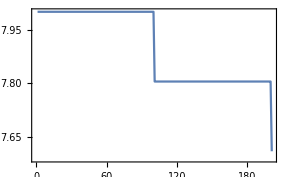

```mathematica
staircase=Table[upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),{k,0,200}];

Length/@Split[staircase]

ListPlot[staircase]
```

## Solve

```mathematica
c=implicitSolveStaircase[m,n,𝔻,{upperLimit,ksStar,α},{Δ𝔼s,tN},a];
```

```mathematica
conc=Table[1.,{j,1,m}];
c=FoldList[solveCV,conc,Range[0,n]];//Timing
c=Rest[c];
```

{5.86 Second,Null}

## Plot staircase voltammogram

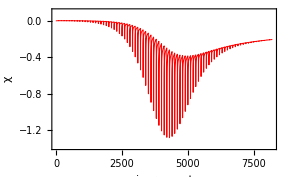

```mathematica
scv1=Map[(((2.+a)*a*#⟦1⟧-((1.+a)^2*#⟦2⟧)+#⟦3⟧)*√((𝔻*(n-1))/(2.*a^2*(1.+a)*𝕥)))&,c];
plot1=ListPlot[scv1,optionA,PlotRange-> {{0,n},{Min[scv1]-0.1,Max[scv1]+0.1}}]
```

```mathematica
convert[i_,{j_}]:={upperLimit-(τ*j),i}
```

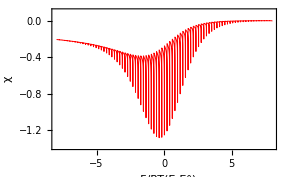

```mathematica
scv2=MapIndexed[convert,scv1];

plot2=ListPlot[scv2,optionB,PlotRange-> {{-8,8},{Min[scv1]-0.1,Max[scv1]+0.1}}]
```

## Moving average filter

Filter data with a moving average filter to remove ac component then re-plot data. If necessary repeat the filtering a second time.

The moving average filter averages over N points with N being the number of increments per cycle.

```mathematica
data2=MovingAverage[scv1,tN];
data2=MovingAverage[data2,tN];
```

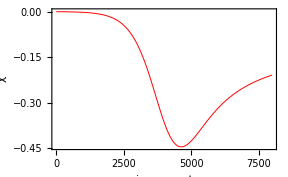

```mathematica
plot3=ListPlot[data2, optionA]
```

The moving average chops the data list. To subtract the unfiltered data, scv1, from the filtered data, data2, we need to align the lists. We do this by first determining the length of the over hang.

```mathematica
Clear[oh];
oh=Length[scv1]-Length[data2]
```

198

```mathematica
convert2[i_,{j_}]:={upperLimit-(oh*τ/2.)-(τ*j),i}
```

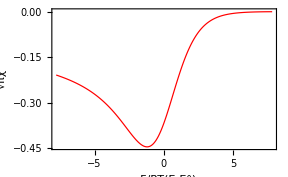

```mathematica
scv3=MapIndexed[convert2,data2];

plot2=ListPlot[scv3,dcOptions]
```

The peak height and peak position are now obtained. Better accuracy is obtained by increasing the magnitude of n.

```mathematica
peakHeight=Min[scv3⟦All,2⟧];
Select[scv3,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at -31.0594 mV with height -0.445932

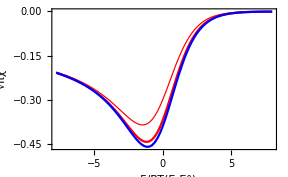

```mathematica
(*current sampled at the end of the step*)
staircaseData=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,tN-1,Length[scv1],tN}];

(*current sampled at 0.33 of the step*)
staircaseData2=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,33,Length[scv1],tN}];

(*current sampled at 0.25 of the step*)
staircaseData3=Table[{upperLimit-(Δ𝔼s*((k-Mod[k,tN])/tN)),scv1⟦k⟧},{k,25,Length[scv1],tN}];

plot2a=ListPlot[staircaseData,dcOptions];
plot2b=ListPlot[staircaseData2,PlotStyle-> Red];
plot2c=ListPlot[staircaseData3,PlotStyle-> Blue];

Show[plot2a,plot2b,plot2c,PlotRange->All]
```

## Fourier transform filter

```mathematica
powerSpectrum[a_,{b_}]:={(b-1)/𝕥,a}
```

```mathematica
fourierData=Abs[Fourier[scv1]];
fourierData=MapIndexed[powerSpectrum,fourierData];
```

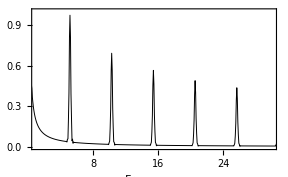

```mathematica
mainPlot=ListPlot[fourierData,optionMain,PlotRange->  {{1,30},{0,1}}]
```

```mathematica
Clear[fourierFilter];

fourierFilter[list_List,x_Integer,y_Integer]:=Module[{a,b},
a=Fourier[list];b=Join[Table[0,{j,1,x-1}],Table[a⟦j⟧,{j,x,y}],Table[0,{j,1,Length[a]-(2*(y+1))}],Table[a⟦j⟧,{j,Length[a]-(y+1),Length[a]-(x-1)}],Table[0,{j,1,x-1}]];Re[InverseFourier[b]]];
```

Convert from dimensionless linear sweep to dimensionless ac by multiplying by 1/(Δ E)√(υ/ω)

#### 1st component

```mathematica
newdata=fourierFilter[scv1,Round[n/tN]-12,Round[n/tN]+12]*Sqrt[f/(2*Pi*Δ𝔼s)];

(*add dimensionless potential scale to the x axis*)

firstComponent=MapThread[{#1⟦1⟧,#2}&,{scv2,newdata}];
```

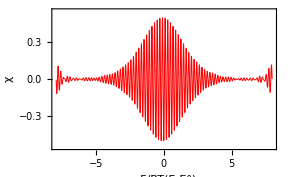

```mathematica
firstComponentPlot=ListPlot[firstComponent,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata]-0.05,Max[newdata]+0.05}}]
```

#### 2nd component

```mathematica
newdata2=fourierFilter[scv1,2*Round[n/tN]-11,2*Round[n/tN]+11]*Sqrt[f/(2*Pi*Δ𝔼s)];

(*add dimensionless potential scale to the x axis*)

secondComponent=MapThread[{#1⟦1⟧,#2}&,{scv2,newdata2}];
```

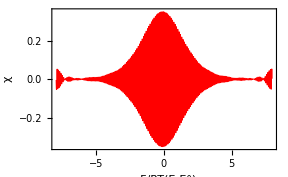

```mathematica
secondComponentPlot=ListPlot[secondComponent,optionB,PlotRange->  {{lowerLimit,upperLimit},{Min[newdata2]-0.001,Max[newdata2]+0.001}}]
```

#### 3rd component

```mathematica
newdata3=fourierFilter[scv1,3*Round[n/tN]-11,3*Round[n/tN]+11]*Sqrt[f/(2*Pi*Δ𝔼s)];

(*add dimensionless potential scale to the x axis*)

thirdComponent=MapThread[{#1⟦1⟧,#2}&,{scv2,newdata3}];
```

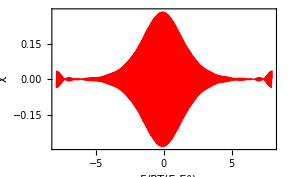

```mathematica
thirdComponentPlot=ListPlot[thirdComponent,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata3]-0.001,Max[newdata3]+0.001}}]
```

#### DC component

```mathematica
newdata4=fourierFilter[scv1,1,35];

(*add dimensionless potential scale to the x axis*)

dcComponent=MapThread[{#1⟦1⟧,#2}&,{scv2,newdata4}];
```

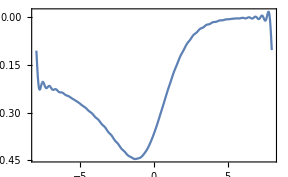

```mathematica
dcComponentPlot=ListPlot[dcComponent]
```